# Rapport projekt inlämning 1

Oliver Rosvall, IX1307, orosvall@kth.se
Namn2 Namnsson, XXXX, namn2@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Hitta lösningarna till polynomekvationen: x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

För att lösa ekvationen x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0 måste vi räkna ut x värderna i ekvationen. Genom att anända vanlig alegrab får man lösningen på x-värderna x_1,x_2,x_3, x_4, x_5:

{-3/2,1,5/2,-√2,√2}

## Visualisering

### Graf över lösning

Nedan följer en graf på ekvationen och dess lösningar markerat i rött.

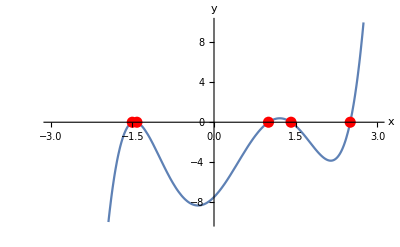

## Kod

Vi berättar för programet att F[x_] är polynomekvationen:

```mathematica
f[x_] =x^5 - 2*x^4 - (19/4)*x^3 + (31/4)*x^2 + (11/2)*x - 15/2
```

Sedan måste vi lösa ekvationen och samtidigt namnger vi lösningarna.

```mathematica
{x1, x2, x3, x4, x5} = x/.Solve [f[x] ==0, x]
```

Därefter användes följande kod för att rita grafen och dess lösningar.

```mathematica
p1 = Plot [f[x],{x,-10, 10},
PlotRange -> {{-3,3}, {-10,10}},
AxesLabel-> {"x", "y"},
Epilog->{PointSize[0.02],Red, Point[{{x1, f[x1]},{x2, f[x2]}, {x3, f[x3]}, {x4, f[x4]}, {x5, f[x5]}}]}]
```

Uppgift 2: Ekvation med absolutbelopp

## Sammanfattning

### Uppgift

Lös ekvationen |x-1|+|x+2|=3 och illustrera lösningsområdet grafiskt.

### Resultat

Med hjälp av Mathematica får vi följande lösning till absolutbeloppet. Det visar sig vara ett intervall mellan -2 till 1 för x-värdet.

-2≤x≤1

## Visualisering

### Lösning av ekvationen

Lösningen på ekvationen kan visualiseras på följande.

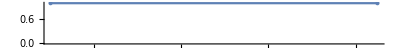

## Kod

```mathematica
ClearAll["`*"]
```

Inför givna data

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Definiera diff.ekvationer och begynnelsevillkor.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Lös diff.ekv.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Exempel för θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

Kurva för variabel vinkel

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

Funktion för sparklängd

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Exempel

```mathematica
len[45°]
```

Tabell för olik vinklar

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Noggrannare data kring maxvärdet.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Sök maxvärde

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

Uppgift 3: Bionomisk ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationen z^7=1-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

Med hjälp av Mathematica får vi sju stycken lösningar. Samtliga lösninga visas nedan:

```mathematica
(1-ⅈ)^(1/7),-(-1)^(1/7)(1-ⅈ)^(1/7),(-1)^(2/7)(1-ⅈ)^(1/7),-(-1)^(3/7)(1-ⅈ)^(1/7),(-1)^(4/7)(1-ⅈ)^(1/7),-(-1)^(5/7)(1-ⅈ)^(1/7),(-1)^(6/7)(1-ⅈ)^(1/7)
```

## Visualisering

### Lösning av ekvationen

Nedan visas lösningarna i ett talplan.

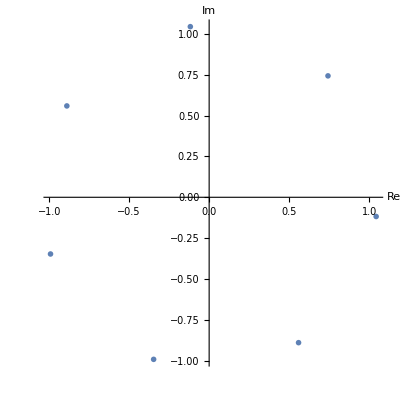

Det visar sig att punkterna är placerade i ett cirkulärt mönster i talplanet.

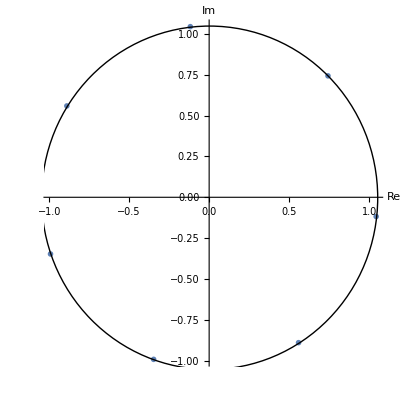

## Kod

För att lösa ekvationen använder vi oss av en solv funktion av ekvationen.

```mathematica
{z1,z2, z3, z4,z5, z6, z7}= z /. Solve [z^7 == 1 - I, z]
```

Därefter skapas en lista över lösningarna denna betecknas cn.

```mathematica
cn={z1,z2, z3, z4,z5, z6, z7}
```

Efter detta skapas en lista av olika talpar (Reella och imaginära), listan betäckans pp.

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i,1,7}]
```

Slutligen används följande kod för att visualisera lösningspunkterna.

```mathematica
ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ Circle[{0,0},  Abs[cn[[1]]]]}]
```

Hjälpmedel

## Hjälpmedel som vi tagit hjälp av

För att lösa dessa uppgifter har vi använt oss av webbsidan Wolframalpha, Wolfram Documentation och även kursmaterial från kursen IX1300.